# Pruebas numéricas sobre la invariancia de la distribución de vectores gaussianos bajo transformaciones unitarias

```mathematica
Needs["CoolTools`"]
```

```mathematica
gaussPDF[x]:= PDF[NormalDistribution[0,1],x]
```

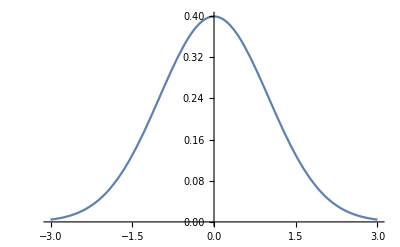

```mathematica
Plot[Evaluate@gaussPDF[x],{x,-3,3}]
```

## Vectores gaussianos reales y transformaciones ortogonales

Primero, revisaremos el caso de vectores gaussianos reales. El caso más sencillo es el de dimensión 2. Tomaremos vectores gaussianos reales bidimensionales, cuya distribución normal estándar deberá mantenerse aún si se les aplica una transformación ortogonal.

```mathematica
generalOrthogonalMatrix[theta_]:= {{Cos[theta],-Sin[theta]},{Sin[theta],Cos[theta]}}
```

```mathematica
gaussianRealSample = RandomVariate[NormalDistribution[0,1],{10000,2}];
```

```mathematica
transformedGaussianRealSample = Map[(generalOrthogonalMatrix[Pi].#)&, gaussianRealSample];
```

```mathematica
gaussianRealSampleX = Map[#[[1]]&, gaussianRealSample];
```

```mathematica
gaussianRealSampleY = Map[#[[2]]&, gaussianRealSample];
```

```mathematica
transformedGaussianRealSampleX = #[[1]]& /@ transformedGaussianRealSample;
```

```mathematica
transformedGaussianRealSampleY = #[[2]]& /@ transformedGaussianRealSample;
```

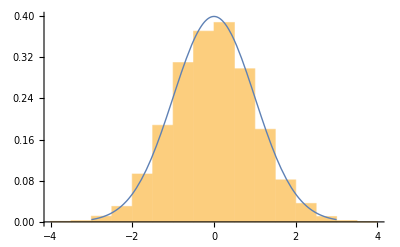
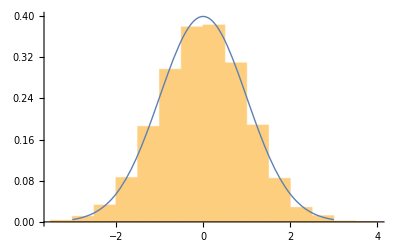

```mathematica
Show[#,Plot[Evaluate@gaussPDF[x],{x,-3,3},PlotStyle->Thick]]& /@ {Histogram[gaussianRealSampleX,Automatic,"PDF"], 
Histogram[gaussianRealSampleY,Automatic,"PDF"]}
```

```mathematica
{DistributionFitTest[gaussianRealSampleX,NormalDistribution[0,1]], DistributionFitTest[gaussianRealSampleY,NormalDistribution[]]}
```

{0.146725,0.669205}

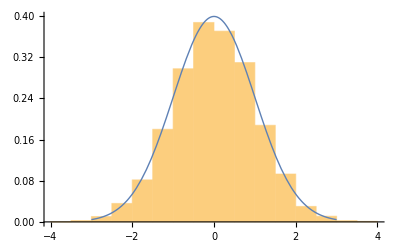
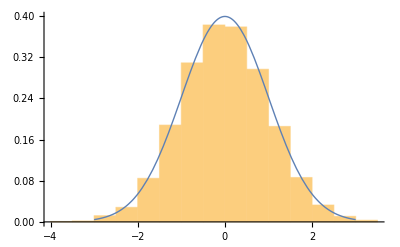

```mathematica
Show[#,Plot[Evaluate@gaussPDF[x],{x,-3,3},PlotStyle->Thick]]& /@ {Histogram[transformedGaussianRealSampleX,Automatic,"PDF"], 
Histogram[transformedGaussianRealSampleY,Automatic,"PDF"]}
```

```mathematica
{DistributionFitTest[transformedGaussianRealSampleX], DistributionFitTest[transformedGaussianRealSampleY]}
```

{0.477335,0.372459}

## Vectores gaussianos complejos y transformaciones unitarias

Ahora lo mismo, pero con vectores complejos y transformaciones unitarias

```mathematica
generalUnitaryMatrix[ϕ_, ϕ1_ , ϕ2_,θ_]:= Exp[I ϕ/2] {{Exp[I ϕ1] Cos[θ],Exp[I ϕ2] Sin[θ]},{-Exp[-I ϕ2] Sin[θ],Exp[-I ϕ1] Cos[θ]}}
```

```mathematica
(*gaussianComplexSample = randomKets[2,2000];*)
gaussianComplexSample = Table[Apply[Complex,RandomReal[NormalDistribution[],{2,2}],{1}],1000]; 
gaussianComplexSampleXRe = Re[#[[1]]& /@ gaussianComplexSample];
gaussianComplexSampleYRe = Re[#[[2]]& /@ gaussianComplexSample];
gaussianComplexSampleXIm = Im[#[[1]]& /@ gaussianComplexSample];
gaussianComplexSampleYIm = Im[#[[2]]& /@ gaussianComplexSample];
```

```mathematica
gaussianComplexSample[[1]]
```

{-0.874112-0.568013 ⅈ,-0.310458-1.68249 ⅈ}

```mathematica
transformedGaussianComplexSample = Map[(generalUnitaryMatrix[0,Pi/2,0,Pi].#)&,gaussianComplexSample];
transformedGaussianComplexSampleXRe = Re[#[[1]]& /@ transformedGaussianComplexSample];
transformedGaussianComplexSampleYRe = Re[#[[2]]& /@ transformedGaussianComplexSample];
transformedGaussianComplexSampleXIm = Im[#[[1]]& /@ transformedGaussianComplexSample];
transformedGaussianComplexSampleYIm = Im[#[[2]]& /@ transformedGaussianComplexSample];
```

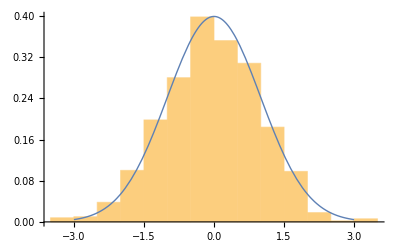
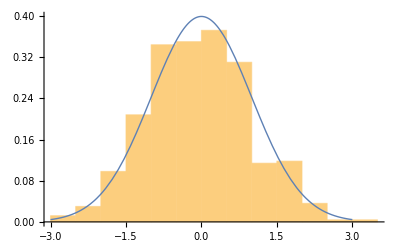
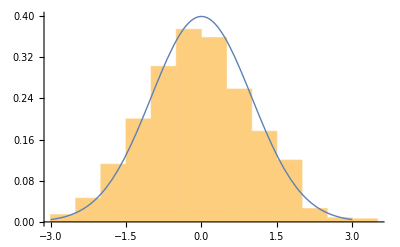
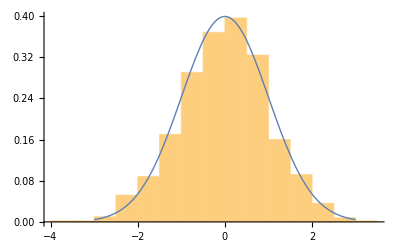

```mathematica
Show[#,Plot[Evaluate@gaussPDF[x],{x,-3,3},PlotStyle->Thick]]& /@ {Histogram[gaussianComplexSampleXRe,Automatic,"PDF"],
Histogram[gaussianComplexSampleYRe,Automatic,"PDF"],
Histogram[gaussianComplexSampleXIm,Automatic,"PDF"],
Histogram[gaussianComplexSampleYIm,Automatic,"PDF"]}
```

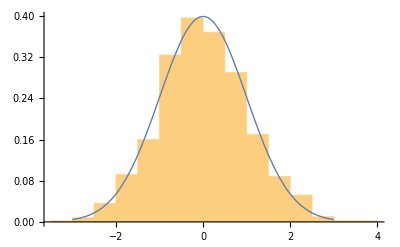
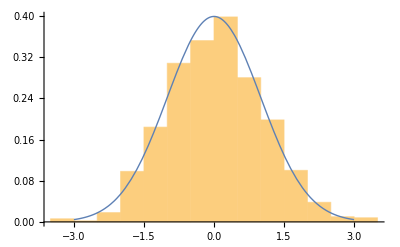
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Show[#,Plot[Evaluate@gaussPDF[x],{x,-3,3}, PlotStyle->Thick]]& /@ {Histogram[transformedGaussianComplexSampleXRe,Automatic,"PDF"],
Histogram[transformedGaussianComplexSampleYRe,Automatic,"PDF"],
Histogram[transformedGaussianComplexSampleXIm,Automatic,"PDF"],
Histogram[transformedGaussianComplexSampleYIm,Automatic,"PDF"]}
```

```mathematica
{DistributionFitTest[gaussianComplexSampleYIm,NormalDistribution[],Automatic]}
```

{0.975982}

```mathematica
{DistributionFitTest[transformedGaussianComplexSampleYIm,NormalDistribution[],Automatic]}
```

{0.0655666}